(*The Convention of this Notebook is that for a state|000>, the first 0 stands for qubit '2', and the last '0' for qubit '0' etc.  Thus to NOT the first qubit, while hadamarding the third means you tensor product the operators as such: H⊗I⊗X *)
(*I really should turn this into a proper package, for now, evaluate the single line below, and head to the bottom of the notebook for an example quantum circuit*)

```mathematica
(*Global*)
q = .; (*Number of Qubits*)
n = .; (*Dimension of statespace*)
all =.; (*used to simplify performing operation on all qubits*)
Sieve=.;
bases=.;
state=.;
(*Useful definitions*)
Tensor[a_,b_]:=Return[KroneckerProduct[a,b]]
px = PauliMatrix[1]; (*Pauli Matrices*)
py = PauliMatrix[2];
pz = PauliMatrix[3];
ph[ϕ_]:=Return[{{1,0},{0,Exp[I ϕ]}}]
H = (pz+px)/Sqrt[2]; (*Hadamard*)
Id1 =IdentityMatrix[1]; 
Id2 =IdentityMatrix[2];
zero={{1},{0}};
one = {{0},{1}};
ZERO = {{1},{0}}.Transpose[{{1},{0}}]; (*|0><0|*)
ONE = {{0},{1}}.Transpose[{{0},{1}}]; (*|1><1|*)
AllSatisfy[expr_,cond_]:=Length@Select[expr,cond]==Length@expr
RX[θ_]:= Return[MatrixExp[-I px θ/2]]
RY[θ_] := Return[MatrixExp[-I py θ/2]]
RZ[θ_] := Return[MatrixExp[-I pz θ/2]]
(*Global Setter Function*)
Qubits[Q_]:= Module[{i,k},q=Q; n=2^Q; all = Range[Q];Sieve=Transpose[Table[Mod[Floor[i/2^(Range[Q]-1)],2],{i,0,2^Q-1}]]; 
bases=Table[{},{j,q}];
For[k=1,k≤ q,k++,
For[i = 1; , i≤2^k , i++,
AppendTo[bases[[k]],StringRiffle[Reverse[Table[Transpose[Reverse[Sieve][[i;;q]]][[1;;n/2^(i-1)]],{i,1,q}]][[k,i]],""]]
];
];
Table[ToExpression["q"<>ToString[i] <>"="<>ToString[i+1]] ,{i,0,Q-1}];
state = zero;
PTL0= Transpose[zero];
PTR0= zero;
PTL1= Transpose[one];
PTR1= one;
For[i=2, i≤ Q, i++, 
state = Tensor[state,zero ]//Flatten;
PTL0 = Tensor[PTL0,Id2];
PTR0 = Tensor[Id2,PTR0];
PTL1 = Tensor[PTL1,Id2];
PTR1 = Tensor[Id2,PTR1];
](*Good to know Kronecker product is actually outer product in Mathematica, hence //Flatten*)
]
(*Gates are functions that generate a matrix*)
(*NOT's qubits given as a list of arguments, eg NOT[1], NOT[{1,3}] == NOT[1].NOT[3] etc.*)
NOT[qbit_]:=Module[{curr = Id1,bits = Sort[DeleteDuplicates[{qbit}//Flatten]],i},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]],
For[i =1, i≤ q,i++, If[ContainsAny[bits,{i}],curr =Tensor[px,curr],curr =Tensor[Id2,curr]]]
,Print["ERROR Invalid Qubit Specified"]
];
Return[curr, Module]
]
Y[qbit_]:=Module[{curr = Id1,bits = Sort[DeleteDuplicates[{qbit}//Flatten]],i},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]],
For[i =1, i≤ q,i++, If[ContainsAny[bits,{i}],curr =Tensor[py,curr],curr =Tensor[Id2,curr]]]
,Print["ERROR Invalid Qubit Specified"]
];
Return[curr, Module]
]
Z[qbit_]:=Module[{curr = Id1,bits = Sort[DeleteDuplicates[{qbit}//Flatten]],i},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]],
For[i =1, i≤ q,i++, If[ContainsAny[bits,{i}],curr =Tensor[pz,curr],curr =Tensor[Id2,curr]]]
,Print["ERROR Invalid Qubit Specified"]
];
Return[curr, Module]
]
(*Hadamard's qubits given as a list of arguments, eg HAD[1], HAD[{1,3}] etc.*)
HAD[qbit_]:=Module[{curr = Id1,bits = Sort[DeleteDuplicates[{qbit}//Flatten]],i},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]],
For[i =1, i≤ q,i++, If[ContainsAny[bits,{i}],curr =Tensor[H,curr],curr =Tensor[Id2,curr]]]
,Print["ERROR Invalid Qubit Specified"]
];
Return[curr, Module]
]
Ph[qbit_,θ_]:=Module[{curr=Id1,bits=Sort[DeleteDuplicates[{qbit}//Flatten]],i},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]],
For[i =1, i≤q,i++, If[ContainsAny[bits,{i}],curr =Tensor[ph[θ],curr],curr =Tensor[Id2,curr]]]
,Print["ERROR Invalid Qubit Specified"]
];
Return[curr, Module]
]
(*Rotate's qubits given as a list, by angle θ, eg ROT[1,π], ROT[{1,3}, π/2] etc.*)
ROTX[qbit_,θ_]:=Module[{curr=Id1,bits=Sort[DeleteDuplicates[{qbit}//Flatten]],i},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]],
For[i =1, i≤q,i++, If[ContainsAny[bits,{i}],curr =Tensor[RX[θ],curr],curr =Tensor[Id2,curr]]]
,Print["ERROR Invalid Qubit Specified"]
];
Return[curr, Module]
]
ROTY[qbit_,θ_]:=Module[{curr=Id1,bits=Sort[DeleteDuplicates[{qbit}//Flatten]],i},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]],
For[i =1, i≤q,i++, If[ContainsAny[bits,{i}],curr =Tensor[RY[θ],curr],curr =Tensor[Id2,curr]]]
,Print["ERROR Invalid Qubit Specified"]
];
Return[curr, Module]
]
ROTZ[qbit_,θ_]:=Module[{curr=Id1,bits=Sort[DeleteDuplicates[{qbit}//Flatten]],i},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]],
For[i =1, i≤q,i++, If[ContainsAny[bits,{i}],curr =Tensor[RZ[θ],curr],curr =Tensor[Id2,curr]]]
,Print["ERROR Invalid Qubit Specified"]
];
Return[curr, Module]
]
(*Controlled Not on qubit, controlled by con: CX[1,3] performs a controlled not on qubit 1 depending on the value of qubit 3*)
CX[qbit_,con_]:=Module[{term1 = Id1,term2 = Id1,bits = Sort[DeleteDuplicates[{qbit,con}//Flatten]],i},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]] && Length[bits]== 2,
For[i =1, i≤ q,i++, 
If[ContainsAny[bits,{i}],If[i== con,term1 =Tensor[ZERO,term1];term2 =Tensor[ONE,term2],term1 =Tensor[Id2,term1];term2 =Tensor[px,term2] ;],
term1 =Tensor[Id2,term1];term2 =Tensor[Id2,term2]
]
]
,Print["ERROR Invalid Qubit Specification for CX gate"]
];
Return[(term1+term2), Module]
]
CH[qbit_,con_]:=Module[{term1 = Id1,term2 = Id1,bits = Sort[DeleteDuplicates[{qbit,con}//Flatten]],i},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]] && Length[bits]== 2,
For[i =1, i≤q,i++, 
If[ContainsAny[bits,{i}],If[i== con,
term1 =Tensor[ZERO,term1];term2 =Tensor[ONE,term2],
term1 =Tensor[Id2,term1];term2 =Tensor[H,term2] ;],
term1 =Tensor[Id2,term1];term2 =Tensor[Id2,term2]
]
],Print["ERROR Invalid Qubit Specification for CH gate"]
];
Return[(term1+term2), Module]
]
CPh[qbit_,con_, θ_]:=Module[{term1 = Id1,term2 = Id1,bits = Sort[DeleteDuplicates[{qbit,con}//Flatten]],i},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]] && Length[bits]== 2,
For[i =1, i≤q,i++, 
If[ContainsAny[bits,{i}],If[i== con,term1 =Tensor[ZERO,term1];term2 =Tensor[ONE,term2],term1 =Tensor[Id2,term1];term2 =Tensor[ph[θ],term2] ;],term1 =Tensor[Id2,term1];term2 =Tensor[Id2,term2]
]
]
,Print["ERROR Invalid Qubit Specification for CROTX gate"]
];
Return[(term1+term2), Module]
]
CROTX[qbit_,con_, θ_]:=Module[{term1 = Id1,term2 = Id1,bits = Sort[DeleteDuplicates[{qbit,con}//Flatten]],i},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]] && Length[bits]== 2,
For[i =1, i≤q,i++, 
If[ContainsAny[bits,{i}],If[i== con,term1 =Tensor[ZERO,term1];term2 =Tensor[ONE,term2],term1 =Tensor[Id2,term1];term2 =Tensor[RX[θ],term2] ;],term1 =Tensor[Id2,term1];term2 =Tensor[Id2,term2]
]
]
,Print["ERROR Invalid Qubit Specification for CROTX gate"]
];
Return[(term1+term2), Module]
]
CROTY[qbit_,con_, θ_]:=Module[{term1 = Id1,term2 = Id1,bits = Sort[DeleteDuplicates[{qbit,con}//Flatten]],i},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]] && Length[bits]== 2,
For[i =1, i≤q,i++, 
If[ContainsAny[bits,{i}],If[i== con,term1 =Tensor[ZERO,term1];term2 =Tensor[ONE,term2],term1 =Tensor[Id2,term1];term2 =Tensor[RY[θ],term2] ;],term1 =Tensor[Id2,term1];term2 =Tensor[Id2,term2]
]
]
,Print["ERROR Invalid Qubit Specification for CROTY gate"]
];
Return[(term1+term2), Module]
]
CROTZ[qbit_,con_, θ_]:=Module[{term1 = Id1,term2 = Id1,bits = Sort[DeleteDuplicates[{qbit,con}//Flatten]],i},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]] && Length[bits]== 2,
For[i =1, i≤q,i++, 
If[ContainsAny[bits,{i}],If[i== con,term1 =Tensor[ZERO,term1];term2 =Tensor[ONE,term2],term1 =Tensor[Id2,term1];term2 =Tensor[RZ[θ],term2] ;],term1 =Tensor[Id2,term1];term2 =Tensor[Id2,term2]
]
]
,Print["ERROR Invalid Qubit Specification for CROTZ gate"]
];
Return[(term1+term2), Module]
]
(*Controlled Controlled Not, only works for a single qubit input currently*)
CCH[qbit_,con1_,con2_]:=Module[{term1 = Id1,term2 = Id1,term3 = Id1,term4 = Id1,bits = Sort[DeleteDuplicates[{qbit,con1,con2}//Flatten]],i},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]] && Length[bits]== 3,
For[i =1, i≤ q,i++,
If[ContainsAny[bits,{i}],
If[i== con1 ,
term1 =Tensor[ZERO,term1];
term2 =Tensor[ONE,term2];
term3 = Tensor[ZERO,term3];
 term4 =Tensor[ONE,term4],
(*Not con1, is it con2?*)
If[i== con2,
term1 =Tensor[ZERO,term1];
term2 =Tensor[ZERO,term2];
term3 = Tensor[ONE,term3];
 term4 =Tensor[ONE,term4],
(*Not con2 or con1, must be qbit*)
term1 =Tensor[Id2,term1];term2 =Tensor[Id2,term2] ;term3 =Tensor[Id2,term3];term4 =Tensor[H,term4] ;]],
(*Happen if current register i is not involved in the CCX*)
term1 =Tensor[Id2,term1];term2 =Tensor[Id2,term2];term3 =Tensor[Id2,term3];term4 =Tensor[Id2,term4]
]
]
,Print["ERROR Invalid Qubit Specification for CCH gate"]
];
Return[term1+term2+term3+term4, Module]
]
(*Controlled Controlled Not, only works for a single qubit input currently*)
CCX[qbit_,con1_,con2_]:=Module[{term1 = Id1,term2 = Id1,term3 = Id1,term4 = Id1,bits = Sort[DeleteDuplicates[{qbit,con1,con2}//Flatten]], i},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]] && Length[bits]== 3,
For[i =1, i≤ q,i++,
If[ContainsAny[bits,{i}],
If[i== con1 ,
term1 =Tensor[ZERO,term1];
term2 =Tensor[ONE,term2];
term3 = Tensor[ZERO,term3];
 term4 =Tensor[ONE,term4],
(*Not con1, is it con2?*)
If[i== con2,
term1 =Tensor[ZERO,term1];
term2 =Tensor[ZERO,term2];
term3 = Tensor[ONE,term3];
 term4 =Tensor[ONE,term4],
(*Not con2 or con1, must be qbit*)
term1 =Tensor[Id2,term1];term2 =Tensor[Id2,term2] ;term3 =Tensor[Id2,term3];term4 =Tensor[px,term4] ;]],
(*Happen if current register i is not involved in the CCX*)
term1 =Tensor[Id2,term1];term2 =Tensor[Id2,term2];term3 =Tensor[Id2,term3];term4 =Tensor[Id2,term4]
]
]
,Print["ERROR Invalid Qubit Specification for CCX gate"]
];
Return[term1+term2+term3+term4, Module]
]
ControlGate[qbit_,control_,gate_]:=Module[{terms = Table[Id1,{count,1,2^Length[control]}],COUNT=1,bits = Sort[DeleteDuplicates[{control,qbit}//Flatten]],i,j},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]] && Length[bits]==Length[control]+1 && Length[bits]≤ q,
For[i =1, i≤ q,i++,
If[ContainsAny[bits,{i}],
If[i≠qbit ,
For[j=1,j≤ Length[terms],j++,
terms[[j]]=Tensor[Sieve[[COUNT,1;;2^Length[control]]][[j]]*ONE+(1-Sieve)[[COUNT,1;;2^Length[control]]][[j]]*ZERO,terms[[j]] ];
];
 COUNT=COUNT+1,
(*Else i == qbit*)
For[j=1,j< Length[terms],j++,
terms[[j]]=Tensor[Id2,terms[[j]]];
];
terms[[Length[terms]]]=Tensor[gate,terms[[Length[terms]]]]
](*If qbit*)
,(*Else, regular bit*)
(*Happens if current register i is not involved in the Control multi-gate*)
For[j=1,j≤ Length[terms],j++,
terms[[j]]=Tensor[Id2,terms[[j]]];
]
](*If contains*)
](*Loop through bits*)
,(*Else ERROR*)Print["ERROR Invalid Qubit Specification for ControlGate gate"]
];
Return[Total[terms], Module]
]
CNOT[qbit_,control_]:=ControlGate[qbit,control,px]
CHAD[qbit_,control_]:=ControlGate[qbit,control,H]
SWAP[q1_,q2_]:= Module[{curr = IdentityMatrix[n]},If[q1 ≠ q2, curr=CX[q1,q2].CX[q2,q1].CX[q1,q2]];Return[curr]]

CSWAP[q1_,q2_,control_]:= CCX[q1,q2,control].CCX[q2,q1,control].CCX[q1,q2,control]
(*Recall The matrix multiplication is backwards from the circuit presentation, since rightmost operators act first.*)
XOR[q1_,q2_]:= CX[q1,q2]
(*We store q2^q3 in q1*)
AND[q1_,q2_,q3_] := CCX[q1,q2,q3]
OR[q1_,q2_,q3_]:= NOT[{q1,q2,q3}].CCX[q1,q2,q3].NOT[{q2,q3}]
NAND[q1_,q2_,q3_]:= NOT[q1].CCX[q1,q2,q3]
NOR[q1_,q2_,q3_] := NOT[q1].OR[q1,q2,q3]
(*Using worker qbit q5, we store q2^q3^q4 in q1*)
AND3[q1_,q2_,q3_,q4_,q5_] := CCX[q1,q4,q5].CCX[q5,q2,q3]
OR3[q1_,q2_,q3_,q4_,q5_]:= OR[q1,q4,q5].OR[q5,q2,q3]
CAND3[q1_,q2_,q3_,q4_,q5_,control_] := ControlGate[q1,{q4,q5,control},px].ControlGate[q5,{q2,q3,control},px]
Reset[state_,qubit_]:=Module[{swap = False, tempstate},If[qubit ≠  q,swap = True]; If[swap,tempstate = SWAP[qubit,q].state, tempstate=state];tempstate = Tensor[zero,Table[Exp[(Phase[tempstate[[i]]]-Phase[tempstate[[i+n/2]]])  * I //FullSimplify](Sqrt[Abs[tempstate[[i]]]^2+Abs[tempstate[[i+n/2]]]^2]) //FullSimplify,{i,1,n/2}]//Flatten
]//Flatten;If[swap,tempstate = SWAP[qubit,q].tempstate];
Return[tempstate,Module]
]
RESET[state_,qubits_]:=Module[{tempstate=state, i},If[Length[qubits]== 0,tempstate=Reset[tempstate,qubits],For[i = 1, i≤ Length[qubits],i++, tempstate = Reset[tempstate, qubits[[i]]]]];
Return[tempstate,Module]
]
(*Quick and dirty QFT implimentation*)
nQFT[numqbits_,sign_]:=Module[{gate=IdentityMatrix[2^numqbits],ω=Exp[2 I π/2^numqbits]},
For[i=0,i<2^numqbits,i++,
For[j=0,j<2^numqbits,j++,
gate[[i+1,j+1]]= 1/Sqrt[2^numqbits] ω^(sign*i*j)
];
];
For[i=q-numqbits,i>0,i--,
gate=Tensor[Id2,gate]
];
Return[gate]
]
QFT[qbits_,sign_]:=Module[{swaps={},bits = DeleteDuplicates[{qbits}//Flatten],i,j,vals=Range[q],temp=1, actual=1, preswap=IdentityMatrix[n],postswap=IdentityMatrix[n], curr},If[AllSatisfy[bits,LessEqualThan[q]]&&AllSatisfy[bits,GreaterThan[0]] && (sign*sign==1),
AppendTo[swaps,SWAP[1,bits[[1]]]];
vals[[1]]=bits[[1]];
vals[[bits[[1]]]]=1;
For[i =2, i≤ Length[bits],i++, 
actual=Position[vals,bits[[i]]][[1,1]];
AppendTo[swaps,SWAP[i,actual]];
temp=vals[[i]];
vals[[i]]=bits[[i]];
vals[[actual]]=temp;
];
For[i = 1, i≤ Length[swaps],i++,
preswap= swaps[[i]].preswap;
postswap= swaps[[Length[swaps]+1-i]].postswap;
];
curr=postswap.nQFT[Length[bits],sign].preswap
,Print["ERROR Invalid Qubit Specified, or invalid sign entered"]
];
Return[curr]
]
(*The Following functions are not quantum Gates*)
(*Measure states' qbits, shots number of times*)
Measure[state_, shots_, qbits_]:= Module[{Measurements={}, tempstate=state, str="",i,,prob1,j},
For[i= 1, i≤ shots, i++,
For[j=1; str="",j≤ Length[qbits],j++,
prob1=Total[Abs[tempstate*Sieve[[qbits[[j]]]]]^2];
 If[RandomVariate[UniformDistribution[]]≤ prob1,str="1"<>str;tempstate=(tempstate*Sieve[[j]])/Sqrt[prob1],str="0"<>str ;tempstate=tempstate*(1-Sieve[[qbits[[j]]]])/Sqrt[1-prob1]]
];
AppendTo[Measurements,str];
tempstate=state;
];
Return[Measurements,Module]
]
Measure[state_, shots_]:= Return[Measure[state, shots, all]]
Phase[x_]:= If[x == 0, Return[0],Return[Log[x/Size[x]//FullSimplify]/I]]
(*For Plotting Probabilities*)
BarPlot[M_, shots_]:= BarChart[Table[Count[M,Sort[DeleteDuplicates[M]][[i]]]/shots,{i, 1, Length[Sort[DeleteDuplicates[M]]]}], ChartLabels->Table[ToString[Sort[DeleteDuplicates[M]][[i]]],{i, 1, Length[Sort[DeleteDuplicates[M]]]}]]
BarPlot[M_, shots_, all_]:=If[all, Return[BarChart[Table[Count[M,bases[[StringLength[M[[1]]],i]]],{i, 1, 2^StringLength[M[[1]]]}]/shots, ChartLabels->bases[[StringLength[M[[1]]]]]]],Return[BarPlot[M,shots]]]
(*Force a state into 1 or 0*)
ForceMeasure[state_,qbit_,bit_]:=Module[{},If[bit == 0,Return[state*(1-Sieve[[q]])/Sqrt[Total[Abs[state*(1-Sieve[[q]])]^2]],Module],Return[state*(Sieve[[q]])/Sqrt[Total[Abs[state*(Sieve[[q]])]^2]],Module]]]
(*Return length of vector*)
Size[state_]:=Return[Sqrt[Total[Abs[state]^2]] //FullSimplify]
(*Return Density matrix of state*)
Density[state_]:= Module[{State=state//Flatten},Return[Table[{State[[i]]},{i,1,n}].Transpose[Table[{State[[i]]},{i,1,n}]]//FullSimplify, Module]]
Probs[state_,qubits_]:=Module[{probs ={}, prob, i, j,b,MeasStates,Q = Length[qubits]},
For[j=0;MeasStates={},j≤ 2^Q-1,j++,
AppendTo[MeasStates,Reverse[Table[Mod[Floor[j/2^i],2],{i,0,Q-1}]]]
];
For[i = 1,i ≤ 2^Q,i++,
prob=state;
For[j=1,j≤ Q, j++,
prob*=(((-1)^b((1-b)-Sieve[[qubits[[j]]]]))/.{b-> MeasStates[[i,j]]});
];
AppendTo[probs,Total[Abs[prob]^2] //FullSimplify]
];
Return[probs ,Module]
]
ProbPlot[state_]:=BarChart[Abs[state]^2//FullSimplify, ChartLabels->bases[[Max[Log[2,Length[state]],1]]]]
```

```mathematica
(*******************************)
```

```mathematica
QFT[{1,3,4},-1].QFT[{1,3,4},1]
```

curr$63467.curr$63470

```mathematica
(*Instantiate the number of Qbits*)
(*sets state variable to |00...0>*)
Qubits[4]
```

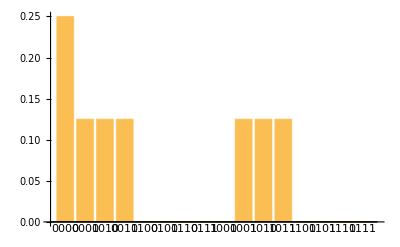

```mathematica
(*qubits are simply identified with integers*)
(*to hadamard qbits 1 and 3, on the state*)
(*All quantum gates are fully upercase modules and return a unitary matrix, which may act on the state by matrix multiplication*)
S=HAD[{1,3}].state;
(*We may perform a controlled not on qubit 4, based on the values of 1,3*)
S=CNOT[4,{1,3}].S;
(*We may perform a quantum fourier transform on selected variable. Order matters for QFTs*)
S=QFT[{1,2,4}].S;
(*We may reset some statevectors qubits selectively*)
S=RESET[S,{3}];
(*We may plot the probabilities of the states*)
ProbPlot[S]
```

```mathematica
(*We may combine this all into one line, which has the usual quirk of matrix multiplication where reading the circuit order of operations should be done right to left*)
S=QFT[{1,2,4}].CNOT[4,{1,3}].HAD[{1,3}].state;
(*A reset is not a quantum gate, so it has to be treated separately*)
S=RESET[S,{3}];
ProbPlot[S]
```

-Graphics-